## 3.029 Spring 2022 Lecture 15 - 03/28/2022

## Chemical Potential Common Tangent

Last lecture, we introduced partial molar quantities, and the tangent-intercept rule

In particular we saw how the chemical potential can be obtained graphically from molar free energy plots

In this lecture, we will investigate miscibility gaps using the common-tangent construction

## Solution Models Overview

Recall the molar GIbbs Free Energy of mixing for an ideal solution, is given simply by the configurational entropy

```mathematica
molarGibbsEnergy["Ideal"][T_,R_:8.314][xB_]=R T ((1-xB) Log[1-xB]+xB Log[xB]);
```

Similarly for the regular solution, we introduce an enthalpic contribution

Where we’ve introduced the  factor we saw last lecture

```mathematica
molarGibbsEnergy["Regular"][ω_,T_,R_:8.314][xB_]=(1-xB) xB ω+R T ((1-xB) Log[1-xB]+xB Log[xB]);
```

Finally, for a general solution model - we additionally introduce activity coefficients in the configurational entropy

This allows us to introduce asymmetric molar Free energies w/ different chemical potentials of the pure compounds

```mathematica
molarGibbsEnergy["General"][γA_,γB_,ω_,T_,R_:8.314][xB_]=(1-xB) xB ω+R T ((1-xB) Log[γA(1-xB)]+xB Log[γB xB]);
```

```mathematica
Manipulate[
Plot[{
molarGibbsEnergy["Ideal"][temperature][xB],
molarGibbsEnergy["Regular"][ω,temperature][xB],
molarGibbsEnergy["General"][γA,γB,ω,temperature][xB]
},{xB,0,1},PlotStyle->Thread[{{Red,Blue,Black},Thick}],Frame->True,LabelStyle->Directive[Black,16],ImageSize->550,PlotLegends->LineLegend[Automatic,{"Ideal Solution Model","Regular Solution Model","General Solution Model"}],FrameLabel->{"Mole Fraction B, x_B","Molar Gibbs Energy, G̲"}],
{{temperature,1},.001,1},
Delimiter,
{{ω,1},-5,5},
Delimiter,
{{γA,0.8},0.5,1.5},{{γB,1.2},0.5,1.5},
Paneled->False,SaveDefinitions->True
]
```

## Common Tangent Construction

Adding enthalpic contributions in  the regular and general solution models above introduces a competition between the configuration entropy at low temperatures, manifesting in the loss of convexity

As we’ve seen before a loss of convexity in thermodynamic potentials suggests a phase transition

In particular, this introduces a range of compositions where the free energy of a single homogeneous solution is higher than the weighted-average of the mechanical mixture of two solutions with the same average composition

As such, the homogenous solution separates into two homogenous solutions with different compositions each to reach equilibrium

At a single temperature, these limiting compositions can be computed with the common tangent construction

Repeating the construction over a range of temperature represents the miscibility gap—boundary of the two-phase region

Similar to L05 and P02, we will compute the common tangent construction numerically using FindRoot and the appropriate equations

where  are the two limiting compositions of the miscibility gap on the A-rich and B-rich phases

```mathematica
chemicalPotentialA["General"][γA_,γB_,ω_,T_,R_:8.314][xB_]=molarGibbsEnergy["General"][γA,γB,ω,T,R][xB]-xB molarGibbsEnergy["General"][γA,γB,ω,T,R]'[xB];
```

First, we want to check if the function indeed loses convexity

We’ll use a built-in function we introduced in L06

```mathematica
convexQ[modelName_][params__]:=FunctionConvexity[{molarGibbsEnergy[modelName][params][xB],1>xB>0},xB]===1
```

```mathematica
convexQ["General"][0.8,1.1,-1,0.25]
```

True

```mathematica
convexQ["General"][0.8,1.1,5,0.25]
```

False

We’ll use a similar lookup-table approach for initial guesses

But notice we now have a multidimensional coordinate space (γA,γB,ω,T)

```mathematica
Clear[commonTangentConstruction,initialGuesses]

initialGuesses["General"]=<|{0.8,1.1,5,0.25}->{0.15,0.85}|>;
commonTangentConstruction[modelName_][params__]:=commonTangentConstruction[modelName][params]=Module[{
reversedGuesses,guessesX,sol},

If[convexQ[modelName][params],Return[{
{-1,2},
molarGibbsEnergy[modelName][params][xB]
}]];

reversedGuesses=AssociationMap[Reverse,initialGuesses[modelName]];
guessesX=First[Nearest[reversedGuesses,{params}]];

sol=Quiet@FindRoot[{
chemicalPotentialA[modelName][params][x1]==chemicalPotentialA[modelName][params][x2],
molarGibbsEnergy[modelName][params]'[x1]==molarGibbsEnergy[modelName][params]'[x2]
},
{x1,guessesX[[1]]},{x2,guessesX[[2]]}];

AssociateTo[initialGuesses[modelName],({params}->{x1,x2})/.sol];
{
{x1,x2}/.sol,
Piecewise[{{molarGibbsEnergy[modelName][params][x1]+molarGibbsEnergy[modelName][params]'[x1] (xB-x1),x2>xB>x1}},molarGibbsEnergy[modelName][params][xB]]/.sol
}
]
```

Let’s see how this looks interactively!

```mathematica
Manipulate[
Block[{pts,func},
{pts,func}=commonTangentConstruction["General"][γA,γB,ω,temperature];
Plot[{func,molarGibbsEnergy["General"][γA,γB,ω,temperature][xB]},{xB,0,1},GridLines->{pts,None},GridLinesStyle->Directive[Gray, Dashed],PlotStyle->{{Red,Thick},{Black,Thick}},Frame->True,LabelStyle->Directive[Black,16],ImageSize->550,PlotLegends->LineLegend[Automatic,{"Common Tangent Construction","General Solution Model"}],FrameLabel->{"Mole Fraction B, x_B","Molar Gibbs Energy, G̲"}]],
{{temperature,0.25},.001,1},
Delimiter,
{{ω,5},-5,5},
Delimiter,
{{γA,0.8},0.5,1.5},{{γB,1.2},0.5,1.5},
Paneled->False
]
```

We can use this to construct a miscibility gap

I.e. concentrations for which the homogeneous solution phase-separates

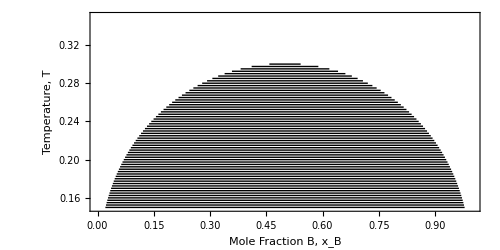

```mathematica
Graphics[Line[Thread[{commonTangentConstruction["General"][0.8,1.1,5,#][[1]],#}]]&/@Join[Range[0.25,0.3,0.0025],Range[0.25- 0.0025,0.15,-0.0025]],AspectRatio->1/2,FrameLabel->{"Mole Fraction B, x_B","Temperature, T"},Frame->True,PlotRange->{{0,1},{0.15,0.35}},PlotRangeClipping->True,ImageSize->500,BaseStyle->18]
```

The miscibility gap indicates the unstable range of compositions the two phases separate.

The composition of each phase is determined by the limits of the miscibility gap.

In order to know the fraction of each phase in the two phase region, the lever rule is used

where the lever lengths are determined by the compositions as

## Convex Hull

In a binary compound, there are more than two competing phases and finding all common tangent constructions between these phases using the previous technique can become cumbersome

Instead, we’ll demonstrate an equivalent technique using the Convex Hull

In-fact, we’ve already seen this when we were exploring the Legendre transform using supporting hyperplanes

Let’s start by defining a binary compound with three phases given by

```mathematica
phase["A"][T_][xB_]=molarGibbsEnergy["General"][0.8,1.1,5,T][xB];
phase["B"][T_][xB_]=molarGibbsEnergy["General"][1.2,1,3,T][xB];
phase["C"][T_][xB_]=molarGibbsEnergy["General"][1,1,5,T][xB];
```

```mathematica
Manipulate[Plot[{
phase["A"][T][xB],
phase["B"][T][xB],
phase["C"][T][xB]
},{xB,0,1},PlotStyle->Thread[{{Red,Blue,Black},Thick}],Frame->True,LabelStyle->Directive[Black,16],ImageSize->550,PlotLegends->LineLegend[Automatic,{"Phase A","Phase B","Phase C"}],FrameLabel->{"Mole Fraction B, x_B","Molar Gibbs Energy, G̲"}],{{T,0.25,"Temperature"},0.1,1},Paneled->False]
```

We are interested in computing the convex-hull of the epigraph of the functions

and more specifically - the minimum of the